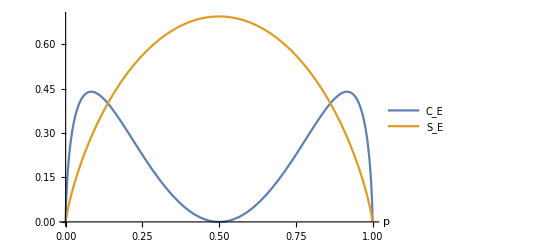

```mathematica
Plot[{p(1-p)(Log[1-p]-Log[p])^2,-p Log[p]-(1-p)Log[1-p]},{p,0,1},AxesLabel->{"p"},PlotLegends->{"C_E","S_E"}]
```

```mathematica
lam0 = p + I q
lam1 = (1-p)-I q
```

p+ⅈ q

1-p-ⅈ q

```mathematica
SE = - (lam0 Log[lam0]+lam1 Log[lam1]);
CE = (lam0 (Log[lam0])^2+lam1 (Log[lam1])^2)-SE^2
```

(1-p-ⅈ q) Log[1-p-ⅈ q]^2+(p+ⅈ q) Log[p+ⅈ q]^2-(-((1-p-ⅈ q) Log[1-p-ⅈ q])-(p+ⅈ q) Log[p+ⅈ q])^2

```mathematica
Manipulate[Plot[{Re[SE]/.{q->q0},Im[SE]/.{q->q0}},{p,0,1},PlotLegends->{"Re SE","Im SE"}],{q0,-2,2}]
```

```mathematica
Manipulate[Plot[{Re[CE]/.{q->q0},Im[CE]/.{q->q0}},{p,0,1},PlotLegends->{"Re CE","Im CE"}],{q0,-2,2}]
```

```mathematica
?Manipulate
```

```mathematica
phi0R = lam0 lam0^(I s) + lam1 lam1^(I s);
phi1R = 1/b1(lam0 (-Log[lam0]-SE)lam0^(I s)+ lam1(-Log[lam1]-SE)lam1^(I s));
b1 = Sqrt[lam0 (-Log[lam0]-SE)^2+lam1(-Log[lam1]-SE)^2];
a0 = - lam0 Log[lam0] - lam1 Log[lam1];
phi0L = Conjugate[lam0] Conjugate[lam0]^(I s) + Conjugate[lam1] Conjugate[lam1]^(I s);
phi1L = 1/c1s(Conjugate[lam0] (-Log[Conjugate[lam0]]-Conjugate[SE])Conjugate[lam0]^(I s)+ Conjugate[lam1](-Log[Conjugate[lam1]]-Conjugate[SE])Conjugate[lam1]^(I s));
c1s = Sqrt[Conjugate[lam0] (-Log[Conjugate[lam0]]-Conjugate[SE])^2+Conjugate[lam1](-Log[Conjugate[lam1]]-Conjugate[SE])^2];
```

```mathematica
CompR = Abs[phi1R]^2/(Abs[phi0R]^2+Abs[phi1R]^2);
CompL = Abs[phi1L]^2/(Abs[phi0L]^2+Abs[phi1L]^2);
```

```mathematica
$Assumptions:={p ∈ Reals && p>0 && q ∈ Reals && s∈ Reals}
```

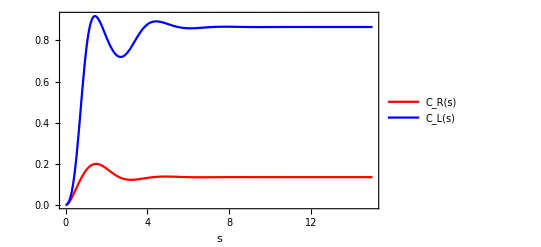

```mathematica
Show[Plot[{CompR/.{p->0.1,q->0.1},CompL/.{p->0.1,q->0.1}},{s,0,15},PlotLegends->{"C_R(s)","C_L(s)"},PlotStyle->{Red,Blue},LabelStyle->Directive[Black, Medium,20]],Frame->True,FrameLabel->{Style["s",20],""},LabelStyle->Directive[Black,Medium,20]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/2level_modular_p_0.1_q_0.1.pdf",%]
```

/Users/aneekphys/Documents/modular plots/2level_modular_p_0.1_q_0.1.pdf

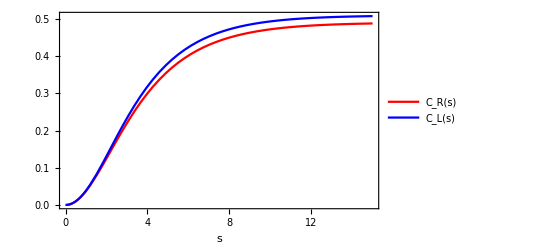

```mathematica
Show[Plot[{CompR/.{p->0.49,q->0.1},CompL/.{p->0.49,q->0.1}},{s,0,15},PlotLegends->{"C_R(s)","C_L(s)"},PlotStyle->{Red,Blue},LabelStyle->Directive[Black, Medium,20]],Frame->True,FrameLabel->{Style["s",20],""},LabelStyle->Directive[Black, Medium,20]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/2level_modular_p_0.49_q_0.1.pdf",%]
```

/Users/aneekphys/Documents/modular plots/2level_modular_p_0.49_q_0.1.pdf

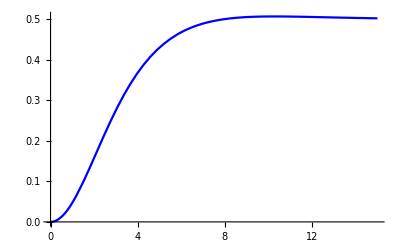

```mathematica
Plot[{(CompR+CompL)/2/.{p->0.45,q->0.1}},{s,0,15},PlotStyle->{Red,Blue}]
```

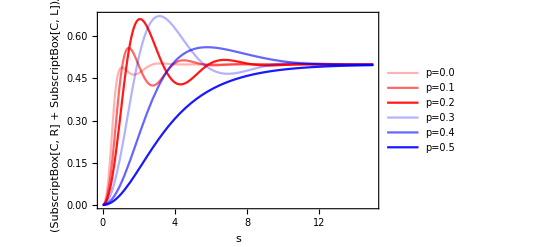

```mathematica
Show[Plot[{(CompR+CompL)/2/.{p->0.0,q->0.1},(CompR+CompL)/2/.{p->0.1,q->0.1},(CompR+CompL)/2/.{p->0.2,q->0.1},(CompR+CompL)/2/.{p->0.3,q->0.1},(CompR+CompL)/2/.{p->0.4,q->0.1},(CompR+CompL)/2/.{p->0.5,q->0.1}},{s,0,15},PlotRange->Full,PlotLegends->{"p=0.0","p=0.1","p=0.2","p=0.3","p=0.4","p=0.5"},PlotStyle->{RGBColor[1,0,0,0.3],RGBColor[1,0,0,0.6],RGBColor[1,0,0,0.9],RGBColor[0,0,1,0.3],RGBColor[0,0,1,0.6],RGBColor[0,0,1,0.9]},LabelStyle->Directive[ Medium,Black,15]],Frame->True,FrameLabel->{Style["s",20,Black],Style["(SubscriptBox[C, R] + SubscriptBox[C, L])/2",20,Black]}]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/2level_modular_av_q_0.1.pdf",%]
```

/Users/aneekphys/Documents/modular plots/2level_modular_av_q_0.1.pdf

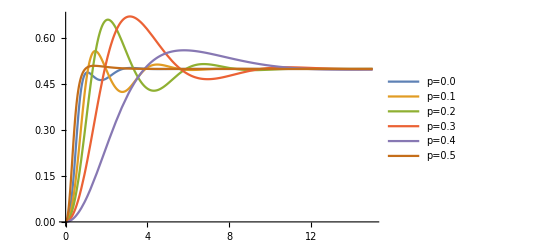

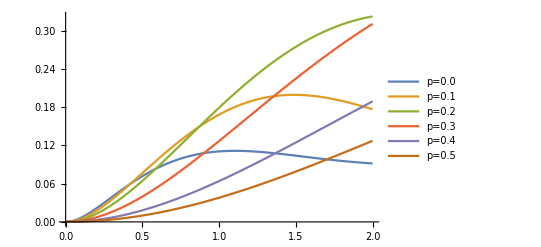

```mathematica
Plot[{CompR/.{p->0.0,q->0.1},CompR/.{p->0.1,q->0.1},CompR/.{p->0.2,q->0.1},CompR/.{p->0.3,q->0.1},CompR/.{p->0.4,q->0.1},CompR/.{p->0.5,q->0.1}},{s,0,2},PlotRange->Full,PlotLegends->{"p=0.0","p=0.1","p=0.2","p=0.3","p=0.4","p=0.5"}]
```

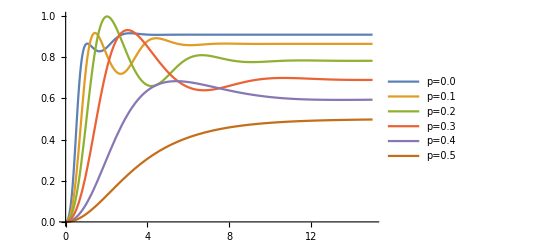

```mathematica
Plot[{CompL/.{p->0.0,q->0.1},CompL/.{p->0.1,q->0.1},CompL/.{p->0.2,q->0.1},CompL/.{p->0.3,q->0.1},CompL/.{p->0.4,q->0.1},CompL/.{p->0.5,q->0.1}},{s,0,15},PlotRange->Full,PlotLegends->{"p=0.0","p=0.1","p=0.2","p=0.3","p=0.4","p=0.5"}]
```

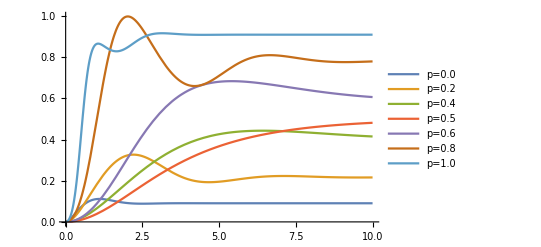

```mathematica
Plot[{CompR/.{p->0.0,q->0.1},CompR/.{p->0.2,q->0.1},CompR/.{p->0.4,q->0.1},CompR/.{p->0.5,q->0.1},CompR/.{p->0.6,q->0.1},CompR/.{p->0.8,q->0.1},CompR/.{p->1.0,q->0.1}},{s,0,10},PlotRange->Full,PlotLegends->{"p=0.0","p=0.2","p=0.4","p=0.5","p=0.6","p=0.8","p=1.0"}]
```

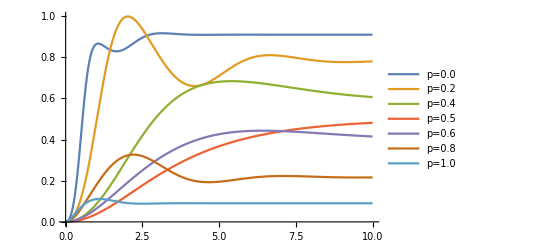

```mathematica
Plot[{CompL/.{p->0.0,q->0.1},CompL/.{p->0.2,q->0.1},CompL/.{p->0.4,q->0.1},CompL/.{p->0.5,q->0.1},CompL/.{p->0.6,q->0.1},CompL/.{p->0.8,q->0.1},CompL/.{p->1.0,q->0.1}},{s,0,10},PlotRange->Full,PlotLegends->{"p=0.0","p=0.2","p=0.4","p=0.5","p=0.6","p=0.8","p=1.0"}]
```

## Changing q

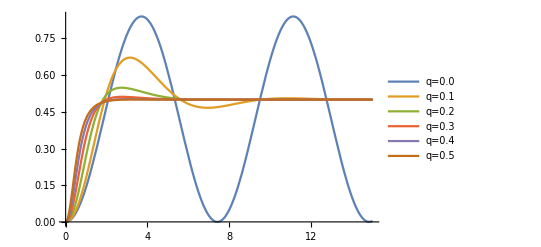

```mathematica
Plot[{(CompR+CompL)/2/.{p->0.3,q->0.0},(CompR+CompL)/2/.{p->0.3,q->0.1},(CompR+CompL)/2/.{p->0.3,q->0.2},(CompR+CompL)/2/.{p->0.3,q->0.3},(CompR+CompL)/2/.{p->0.3,q->0.4},(CompR+CompL)/2/.{p->0.3,q->0.5}},{s,0,15},PlotRange->Full,PlotLegends->{"q=0.0","q=0.1","q=0.2","q=0.3","q=0.4","q=0.5"}]
```

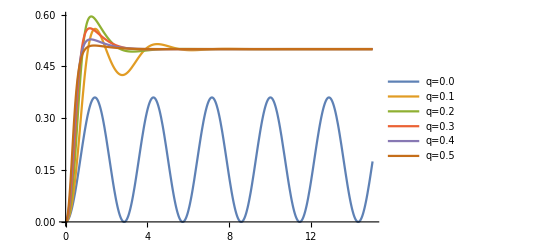

```mathematica
Plot[{(CompR+CompL)/2/.{p->0.1,q->0.0},(CompR+CompL)/2/.{p->0.1,q->0.1},(CompR+CompL)/2/.{p->0.1,q->0.2},(CompR+CompL)/2/.{p->0.1,q->0.3},(CompR+CompL)/2/.{p->0.1,q->0.4},(CompR+CompL)/2/.{p->0.1,q->0.5}},{s,0,15},PlotRange->Full,PlotLegends->{"q=0.0","q=0.1","q=0.2","q=0.3","q=0.4","q=0.5"}]
```

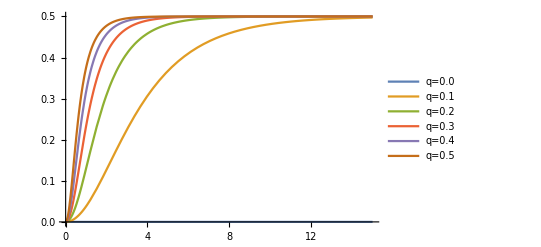

```mathematica
Plot[{(CompR+CompL)/2/.{p->0.5001,q->0.0},(CompR+CompL)/2/.{p->0.5001,q->0.1},(CompR+CompL)/2/.{p->0.5001,q->0.2},(CompR+CompL)/2/.{p->0.5001,q->0.3},(CompR+CompL)/2/.{p->0.5001,q->0.4},(CompR+CompL)/2/.{p->0.5001,q->0.5}},{s,0,15},PlotRange->Full,PlotLegends->{"q=0.0","q=0.1","q=0.2","q=0.3","q=0.4","q=0.5"}]
```

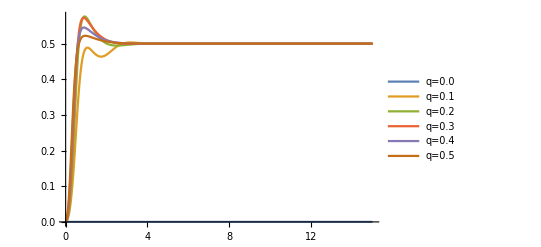

```mathematica
Plot[{(CompR+CompL)/2/.{p->0.0000001,q->0.0},(CompR+CompL)/2/.{p->0.0000001,q->0.1},(CompR+CompL)/2/.{p->0.0000001,q->0.2},(CompR+CompL)/2/.{p->0.0000001,q->0.3},(CompR+CompL)/2/.{p->0.0000001,q->0.4},(CompR+CompL)/2/.{p->0.0000001,q->0.5}},{s,0,15},PlotRange->Full,PlotLegends->{"q=0.0","q=0.1","q=0.2","q=0.3","q=0.4","q=0.5"}]
```

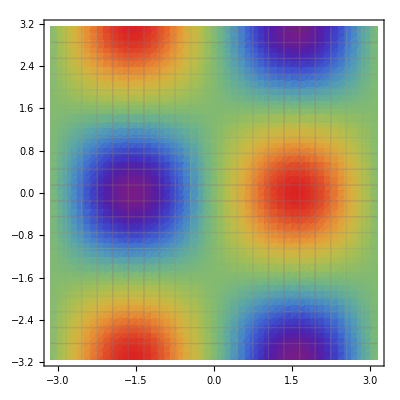

```mathematica
DensityPlot[Sin[x]*Cos[y],{x,-Pi,Pi},{y,-Pi,Pi},ColorFunction->"Rainbow",PlotPoints->50,Mesh->20,PlotRange->All]
```

## Density plots of a_0 = S_E and b_1^2= C_E

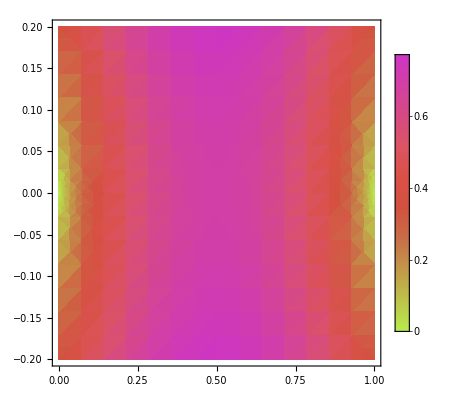

```mathematica
DensityPlot[Re[a0/.{lam0->p + I q,lam1->1-p-I q}],{p,0,1},{q,-0.2,0.2},PlotLegends->Automatic,ColorFunction->"NeonColors",MaxRecursion->15]
```

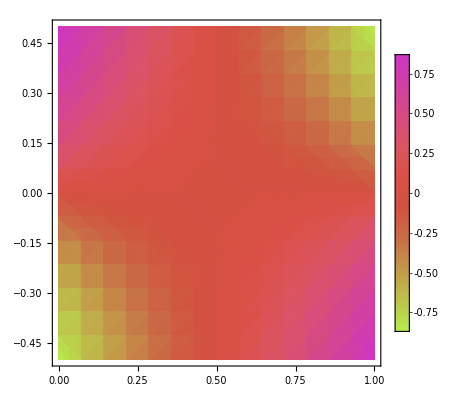

```mathematica
DensityPlot[Im[a0/.{lam0->p + I q,lam1->1-p-I q}],{p,0,1},{q,-0.5,0.5},PlotLegends->Automatic,ColorFunction->"NeonColors",MaxRecursion->15]
```

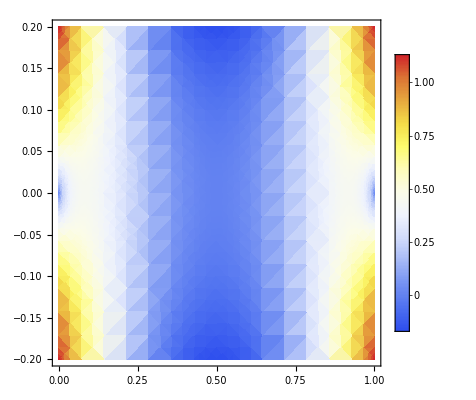

```mathematica
DensityPlot[Re[b1^2/.{lam0->p + I q,lam1->1-p-I q}],{p,0,1},{q,-0.2,0.2},PlotLegends->Automatic,ColorFunction->"TemperatureMap",MaxRecursion->15]
```

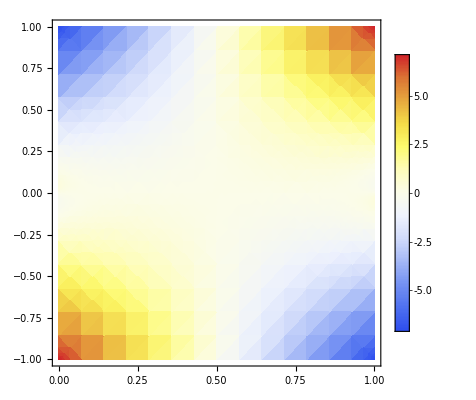

```mathematica
DensityPlot[Im[b1^2/.{lam0->p + I q,lam1->1-p-I q}],{p,0,1},{q,-1,1},PlotLegends->Automatic,ColorFunction->"TemperatureMap",MaxRecursion->15]
```

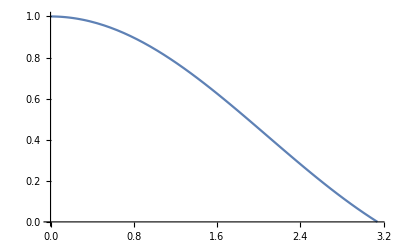

```mathematica
Plot[Sin[x]/x,{x,0,Pi}]
```